# Bell state infidelity

P. Huft

For quantifying the different sources of infidelity when preparing/measuring a Bell state with photons. Often we can account for infidelity as writing the state (for example) as α 10+β01+ϵDwhere the state is maximally entangled for |α|=|β|=1/√2 and ϵ=0. When ϵ!=0, there is some population in an unwanted state D which can be taken as a stand in for several different errors or loss channels.

```mathematica
conj[z_]:=z/.{ⅈ-> -ⅈ,-ⅈ->ⅈ};
SetOptions[Plot,Axes->False,Frame->{True,True,False,False},LabelStyle->Directive[Black, 16],ImageSize->Medium];
```

Finite photon collection from a lens, e.g. when collecting the photons from single atoms with three possible decay polarizations. In reality, we condition the fidelity on reading the appropriate clicks at the detector, so the photon collection efficiency only effects the rate of Bell state preparation, until we also account for SPCM dark counts.

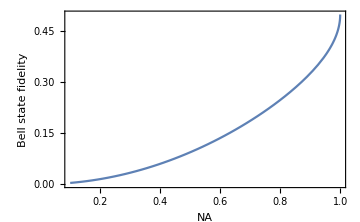

```mathematica
Clear[NA];
pi ={0,-Sin[θ],0};
rh =ⅇ^(ⅈ ϕ)/(√2){0,Cos[θ],ⅈ};
lh =ⅇ^(-ⅈ ϕ)/(√2){0,Cos[θ],-ⅈ};
Map[Integrate[#.conj[#] Sin[θ],{θ,0,π},{ϕ,0,2π}]&,{pi,lh,rh}];
norm = 1/%[[1]];
Psigma=norm Integrate[lh.conj[lh]Sin[θ],{θ,0,ArcSin[NA]},{ϕ,0,2π}];
(*the Bell state expressed in the basis {+,-,-,+,D}. *)
Bell = 1/(√2){1,1,0}; 
(*state prepared with finite photon collection*)
ϵ=√(1-Psigma);
α=β=√((1-ϵ^2)/2);(*valid when α,β,ϵ are real*)
state = ({{α}, {β}, {ϵ}});
Plot[(Bell.state)^2,{NA,0.1,1},FrameLabel->{"NA","Bell state fidelity"}]
```

Fidelity reduction from dark counts on the SPCM. The lens efficiency effects the fidelity when there is a finite rate of dark counts, because this changes the probability that the click we measured was actually the signal. Clearly, as lens efficiency goes to zero, the probability that the click was a dark count goes to one.

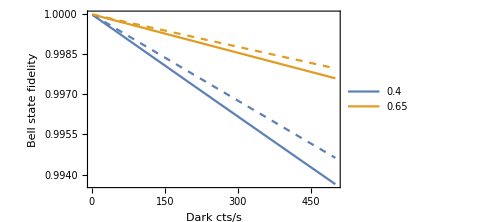

```mathematica
Clear[NA,QE];
τ=10^-7;(*the detection time window [s]*)
Rdc;(*rate of dark counts*)
Bell = 1/(√2){1,1,0}; (*the Bell state expressed in the basis {+,-,-,+,D}. *)
Psigma=norm Integrate[lh.conj[lh]Sin[θ],{θ,0,ArcSin[NA]},{ϕ,0,2π}];(*fraction of σ photons collected*)
Pfc = 0.8;(*fiber coupling*)
(*QE = 0.65;*)(*SPCM quantum efficiency*)
Pph= Psigma*Pfc*QE;(*prob. of detecting a photon from one node. neglects BS/PBS imperfections*)
Pdark1node = τ Rdc;(*prob. that we get a dark count on one of the detectors*)
(*Pdark = (4 Pph Pdark1node)/Pph^2 ;*)
Pdark=(4Pdark1node Pph)/(Pph^2+4Pdark1node Pph) ;(*normalized prob. of getting a dark count at any one of the detectors or two simultaneously*)

ϵ=√Pdark;
α=β=√((1-ϵ^2)/2);(*valid when α,β,ϵ are real*)
state = ({{α}, {β}, {ϵ}});
NAsteps = {0.4,0.65};
plt1=Plot[Evaluate[Table[(Bell.state)^2/.QE->0.65,{NA,NAsteps}]],{Rdc,1,500},FrameLabel->{"Dark cts/s","Bell state fidelity"},PlotLegends->NAsteps];
plt2=Plot[Evaluate[Table[(Bell.state)^2/.QE->0.77,{NA,NAsteps}]],{Rdc,1,500},FrameLabel->{"Dark cts/s","Bell state fidelity"},PlotStyle->Dashed];
Show[plt1,plt2]
```

```mathematica
Pdark/.{NA->0.4,Rdc->100,QE->0.5}
```

0.000416162